Program for validation of the method

The program, which transforms the selected stress tensor into a deviatoric stress tensor, calculates the Lode angle θ and introduces the CPB06 model.
The CPB06 yield surface model has been transformed into a form that depends on θ and the invariant J2 instead of S1, S2 and S3.
This is followed by the calculation of the new J2* and S1*, S2* and S3*. From the principal stresses, we calculate the tensor sij* (transformation with eigenvectors).
Finally, there is the calculation of the new stress tensor σij*, which tells us what the stress tensor on the yield surface would be.

```mathematica
(*Tenzor napetosti, tenzor deviaotričnih napetosti in vse relavantne invariante*)
σij={{σ11,σ12,σ13},{σ12,σ22,σ23},{σ13,σ23,σ33}};
sij={{s11,s12,s13},{s21,s22,s23},{s31,s32,s33}};

For[i=1,i<=3,i++,
For[j=1,j<=3,j++,
For[k=1,k<=3,k++,
sij[[i,j]]=σij[[i,j]]-1/3 Tr[σij]*KroneckerDelta[i,j]
]]]

I1= Tr[σij];
I2 = 1/2*Sum[σij[[i,j]] σij[[j,i]],{i,1,3},{j,1,3}]//FullSimplify;
I3 = 1/3*Sum[σij[[i,j]] σij[[j,k]] σij[[k,i]],{i,1,3},{j,1,3},{k,1,3}]//FullSimplify;

J1= Tr[σij];
J2 = 1/2*Sum[sij[[i,j]]*sij[[j,i]],{i,1,3},{j,1,3}]//FullSimplify;

sij={{10,15,20},{15,-10,5},{20,5,10}};
J3 = 1/3*Sum[sij[[i,j]]*sij[[j,k]]*σij[[k,i]],{i,1,3},{j,1,3},{k,1,3}]//FullSimplify


(* Izračun Lodejevega kota *)
θ= 1/3 ArcCos[(3 √3)/2 *J3/J2^(3/2)]*180/Pi;
(* Izračun glavnih napetosti in glavnih vektorjev *)
nσ = Eigenvectors[σij]//Transpose//N;
σ1 = Eigenvalues[σij][[1]]//N;
σ2 = Eigenvalues[σij][[2]]//N;
σ3 = Eigenvalues[σij][[3]]//N;
σp ={{σ1,0,0},{0,σ2,0},{0,0,σ3}};

ns = Eigenvectors[sij]//Transpose//N;
S1 = Eigenvalues[sij][[1]]//N;
S2 = Eigenvalues[sij][[2]]//N;
S3 = Eigenvalues[sij][[3]]//N;
Sp ={{S1,0,0},{0,S2,0},{0,0,S3}};
```

25/3 (29 σ11+8 σ12+38 σ13+14 σ22+24 σ23+21 σ33)

Na tem mestu smo določili vse pomembne invariante napetostnega in deviatoričnega tenzorja. Določili smo tudi Lodejebv kot. 
Sledi vpeljava modela CPB06 in njegova transormacija. Najprej je potrebno določiti in izbrati parametre modela.

```mathematica
(* Vpeljava parametrov modela CPB06 *)

σT=250;
σC =200;
F =3700;
a =2;
h=((2^a-2(σT/σC)^a)/((2*σT/σC)^a-2))^(1/a);
k1 =(1-h)/(1+h);
 
CPB06[s1_, s2_, s3_] := (Abs[s1]-k s1)^a+(Abs[s2]-k s2)^a+(Abs[s3]-k s3)^a-F
```

```mathematica
(* Glavne deviatorične napetosti lahko izrazimo v odvisnosti od J2 in Lodejevega kota θ *)
S= 2/(√3)*√J2*{{Cos[θ]},{Cos[2 Pi /3-θ]},{Cos[2 Pi /3+θ]}};
(* CPB model zapišemo namesto v odvisnosti od glavnih napetosti  v odvisnosti od J2 in kota θ *)
CPB =((2 √J2)/(√3)Abs[Cos[θ]]-k1 S[[1]])^a+((2 √J2)/(√3)Abs[Cos[2 Pi /3-θ]]-k1 S[[2]])^a+((2 √J2)/(√3)Abs[Cos[2 Pi /3+θ]]-k1 S[[3]])^a-F;
(* Izračunamo novi J2 ki je odvisen od tenorja napetosti in leži na povšrini tečenja CPB06 *)
(* sol = Solve[CPB==0,J2];
J2n ={J2}/.sol[[1]] *)  

(* J2n lahko določimo z izpostavljanjem J2 iz enačbe modela. To lahko storimo z vgrajenimi reševalniki za simbolno reševanje ali pa analitično *)
J2n = 3/4 (F/((Abs[Cos[θ]]-k1*Cos[θ])^a+(Abs[Cos[2 Pi /3+θ]]-k1*Cos[2 Pi /3+θ])^a+(Abs[Cos[2 Pi /3-θ]]-k1*Cos[2 Pi /3-θ])^a))^(2/a);
```

Sledi ponoven izračun novih glavnih deviatoričnih napetosti S1*, S2* in S3*. Za tem bo sledila še transformacija v novi tenzor deviatoričnih napetosti sij* in še transformacija v novi napetosti tenzor σij*

```mathematica
(* Določitev S1*,S2*in S3* *)
J2 = J2n;
Sn = S//Flatten;

(* Izračun novega tenzorja deviatoričnih napetosti sij* *)
Spn ={{Sn[[1]],0,0},{0,Sn[[2]],0},{0,0,Sn[[3]]}};
sijn=ns.Spn.Inverse[ns];

(* Izračun novega tenzorja napetosti σij* *)
σijn = {{σ11,σ12,σ13},{σ12,σ22,σ23},{σ13,σ23,σ33}};
For[i=1,i<=3,i++,
For[j=1,j<=3,j++,
For[k=1,k<=3,k++,
σijn[[i,j]]=sijn[[i,j]]+1/3 Tr[σij]*KroneckerDelta[i,j]
]]]
σijn;
```

Prikaz metode na primeru izbranega napetostnega tenzorja in 3D izris površine tečenja

```mathematica
σij = {{50,30,10},
         {30,25,-15},
         {10,-15,-30}};
σT=300;
σC =-250;
F =12000;
a =2;

For[i=1,i<=3,i++,
For[j=1,j<=3,j++,
For[k=1,k<=3,k++,
sij[[i,j]]=σij[[i,j]]-1/3 Tr[σij]*KroneckerDelta[i,j]
]]]

I1= Tr[σij];
I2 = 1/2*Sum[σij[[i,j]] σij[[j,i]],{i,1,3},{j,1,3}]//FullSimplify;
I3 = σij[[1,1]] (σij[[2,2]] σij[[3,3]]-σij[[2,3]] σij[[2,3]])-σij[[2,2]] σij[[1,3]] σij[[1,3]]-σij[[1,2]] (σij[[3,3]] σij[[1,2]]-2 σij[[1,3]] σij[[2,3]]);
(*I3 = 1/3*Sum[σij[[i,j]] σij[[j,k]] σij[[k,i]],{i,1,3},{j,1,3},{k,1,3}]//FullSimplify;*)

J1= Tr[σij];
J2 = 1/2*Sum[sij[[i,j]]*sij[[j,i]],{i,1,3},{j,1,3}]//FullSimplify;
J3 = sij[[1,1]] (sij[[2,2]] sij[[3,3]]-sij[[2,3]] sij[[2,3]])-sij[[2,2]] sij[[1,3]] sij[[1,3]]-sij[[1,2]] (sij[[3,3]] sij[[1,2]]-2 sij[[1,3]] sij[[2,3]]);
(*J3 = 1/3*Sum[sij[[i,j]]*sij[[j,k]]*sij[[k,i]],{i,1,3},{j,1,3},{k,1,3}]//FullSimplify;*)

(* Izračun Lodejevega kota *)
If[J3>0,
θ=-1/3 ArcCos[(3 √3)/2 *J3/J2^(3/2)]//N,
θ=1/3 ArcCos[(3 √3)/2 *J3/J2^(3/2)]//N]
(* Izračun glavnih napetosti in glavnih vektorjev *)
nσ = Eigenvectors[σij]//Transpose//N;
σ1 = Eigenvalues[σij][[1]]//N;
σ2 = Eigenvalues[σij][[2]]//N;
σ3 = Eigenvalues[σij][[3]]//N;
σp ={{σ1,0,0},{0,σ2,0},{0,0,σ3}};
											(* PAZI NA VRSTNI RED, DODAJ SORT ČE JE PRAVILNO, PREVERI!*)
ns = Eigenvectors[sij]//Transpose//N;
S1 = Eigenvalues[sij][[1]]//N;
S2 = Eigenvalues[sij][[2]]//N;
S3 = Eigenvalues[sij][[3]]//N;
Sp ={{S1,0,0},{0,S2,0},{0,0,S3}};


h=((2^a-2(σT/σC)^a)/((2*σT/σC)^a-2))^(1/a);
k1 =(1-h)/(1+h)//N;

J2n = 3/4 (F/((Abs[Cos[θ]]-k1*Cos[θ])^a+(Abs[Cos[2 Pi /3+θ]]-k1*Cos[2 Pi /3+θ])^a+(Abs[Cos[2 Pi /3-θ]]-k1*Cos[2 Pi /3-θ])^a))^(2/a);

Sn= 2/(√3)*√J2n*{{Cos[θ]},{Cos[2 Pi /3-θ]},{Cos[2 Pi /3+θ]}}//Flatten;

Spn ={{Sn[[1]],0,0},{0,Sn[[2]],0},{0,0,Sn[[3]]}};
sijn=ns.Spn.Inverse[ns];

σijn = {{σ11,σ12,σ13},{σ12,σ22,σ23},{σ13,σ23,σ33}};
For[i=1,i<=3,i++,
For[j=1,j<=3,j++,
For[k=1,k<=3,k++,
σijn[[i,j]]=sijn[[i,j]]+1/3 Tr[σij]*KroneckerDelta[i,j]
]]]

CPB06[s1_, s2_, s3_] := (Abs[s1]-k1 s1)^a+(Abs[s2]-k1 s2)^a+(Abs[s3]-k1 s3)^a-F
CPB063D= ContourPlot3D[CPB06[s1, s2, s3] == 0, {s1, -200, 200}, {s2, -200, 200},{s3, -200, 200},PlotPoints->15,ImageSize->{400,400},ContourStyle->Opacity[0.01],AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,AxesLabel->{"S1","S2","S3"}];
Tocke3D1={{S1,S2,S3}};
Tocke3D2={{Sn[[1]],Sn[[2]],Sn[[3]]}};                (* PAZI NA VRSTNI RED, DODAJ SORT ČE JE PRAVILNO, PREVERI*)

Show[CPB063D,Graphics3D[{Red,PointSize[.025],Point[Tocke3D1]}],Graphics3D[{Blue,PointSize[.025],Point[Tocke3D2]}],ViewProjection->"Orthographic",PlotRange->All,ViewPoint->{1,1,1},AxesOrigin->{0,0,0}]

Print["Prvotne vrednosti tenzorjev in invariant:"]
Print["Originalni tenzor σij =",σij//MatrixForm," MPa"]
Print["Originalni tenzor deviatoričnih napetosti sij =",sij//MatrixForm," MPa"]
Print["Lastni vektorji tenzorja napetosti =",nσ//MatrixForm]
Print["I1 = ",I1," MPa     I2 = ",I2//N," MPa^2     I3 = ",I3," MPa^3"]
Print["J1 = ",J1," MPa     J2 = ",J2," MPa^2     J3 = ",J3," MPa^3"//N]
Print["σ1 = ",σ1," MPa     σ2 = ",σ2," MPa     σ3 = ",σ3//N," MPa"]
Print["S1 = ",S1," MPa     S2 = ",S2," MPa     S3 = ",S3//N, " MPa"]
Print["\nLodejev kot θ = ",θ*180/Pi," °\n"]
Print["Parametri modela CPB06:"]
Print["Da bo k realen mora biti razmerje med nategom in tlakom znotraj intervala: ", 2^((1-a)/a)//N," in ",2^((a-1)/a)//N]
Print["σT = ",σT," MPa     σC = ",σC," MPa     F = ",F, "     k = ",k1,"     a = ",a]
Print["\nNove vrednosti pridobljene iz povšrine tečenja CPB06"]
Print["J2^* = ",J2n," MPa^2"]
Print["S1^* = ",Sn[[1]]," MPa     S2^* = ",Sn[[2]]," MPa     S3^* = ",Sn[[3]]//N, " MPa"]
Print["Novi tenzor deviatoričnih napetosti sij^* =",sijn//MatrixForm," MPa"]
Print["Novi napetostni tenzor σij^* =",σijn//MatrixForm," MPa"]
```

-0.48539

-Graphics3D-

Prvotne vrednosti tenzorjev in invariant:

Originalni tenzor σij =(50 | 30 | 10
30 | 25 | -15
10 | -15 | -30) MPa

Originalni tenzor deviatoričnih napetosti sij =(35 | 30 | 10
30 | 10 | -15
10 | -15 | -45) MPa

Lastni vektorji tenzorja napetosti =(3. | -0.234606 | 1.31153
2. | 0.351909 | -1.96729
0. | 1. | 1.)

I1 = 45 MPa     I2 = 3237.5 MPa^2     I3 = -33250 MPa^3

J1 = 45 MPa     J2 = 2900 MPa^2     J3 = 6875 MPa^3

σ1 = 70. MPa     σ2 = -37.6247 MPa     σ3 = 12.6247 MPa

S1 = 55. MPa     S2 = -52.6247 MPa     S3 = -2.37531 MPa

Lodejev kot θ = -27.8108 °

Parametri modela CPB06:

Da bo k realen mora biti razmerje med nategom in tlakom znotraj intervala: 0.707107 in 1.41421

σT = 300 MPa     σC = -250 MPa     F = 12000     k = 0.293848     a = 2

Nove vrednosti pridobljene iz povšrine tečenja CPB06

J2^* = 5654.96 MPa^2

S1^* = 76.8031 MPa     S2^* = -73.4861 MPa     S3^* = -3.31693 MPa

Novi tenzor deviatoričnih napetosti sij^* =(48.8747 | 41.8926 | 13.9642
41.8926 | 13.9642 | -20.9463
13.9642 | -20.9463 | -62.8389) MPa

Novi napetostni tenzor σij^* =(63.8747 | 41.8926 | 13.9642
41.8926 | 28.9642 | -20.9463
13.9642 | -20.9463 | -47.8389) MPa

Prvotne vrednosti tenzorjev in invariant:

Originalni tenzor σij =(50 | 30 | 10
30 | 25 | -15
10 | -15 | -30) MPa

Originalni tenzor deviatoričnih napetosti sij =(35 | 30 | 10
30 | 10 | -15
10 | -15 | -45) MPa

Lastni vektorji tenzorja napetosti =(3. | -0.234606 | 1.31153
2. | 0.351909 | -1.96729
0. | 1. | 1.)

I1 = 45 MPa     I2 = 3237.5 MPa^2     I3 = -33250 MPa^3

J1 = 45 MPa     J2 = 2900 MPa^2     J3 = 6875 MPa^3

σ1 = 70. MPa     σ2 = -37.6247 MPa     σ3 = 12.6247 MPa

S1 = 55. MPa     S2 = -52.6247 MPa     S3 = -2.37531 MPa

Lodejev kot θ = -27.8108 °

Parametri modela CPB06:

Da bo k realen mora biti razmerje med nategom in tlakom znotraj intervala: 0.707107 in 1.41421

σT = 300 MPa     σC = -250 MPa     F = 12000     k = 0.293848     a = 2

Nove vrednosti pridobljene iz povšrine tečenja CPB06

J2^* = 5654.96 MPa^2

S1^* = 76.8031 MPa     S2^* = -73.4861 MPa     S3^* = -3.31693 MPa

Novi tenzor deviatoričnih napetosti sij^* =(48.8747 | 41.8926 | 13.9642
41.8926 | 13.9642 | -20.9463
13.9642 | -20.9463 | -62.8389) MPa

Novi napetostni tenzor σij^* =(63.8747 | 41.8926 | 13.9642
41.8926 | 28.9642 | -20.9463
13.9642 | -20.9463 | -47.8389) MPa

```mathematica
CPBstress[s1_, s2_, s3_] := (Abs[s1]-k1 s1)^a+(Abs[s2]-k1 s2)^a+(Abs[s3]-k1 s3)^a


Manipulate[Show[ContourPlot3D[CPBstress[s1, s2, s3] == yield, {s1, -400, 400}, {s2, -400, 400},{s3, -400, 400}, Axes -> True,PlotPoints->10,ImageSize->{400,400},ContourStyle->Opacity[0.6],AxesEdge->{{-1,-1},{1,-1},{-1,-1},ViewPoint->Front},Axes->True,AxesLabel->{"S1","S2","S3"}],
 Graphics3D[{Green,PointSize[0.025],Point[{s1,s2,s3}]}],Graphics3D[{Blue,PointSize[0.025],Point[{Sn[[1]],Sn[[2]],Sn[[3]]}]}],Graphics3D[{Red,PointSize[0.025],Point[{S1,S2,S3}]}],PlotRange->All,(*PlotLabel->Row[{"σcpb = ",Text[(Abs[s1]-k1 s1)^a+(Abs[s2]-k1 s2)^a+(Abs[s3]-k1 s3)^a],Text@" MPa","."}], ViewProjection->"Orthographic",*)PlotRange->All,ViewPoint->{1,1,1},AxesOrigin->{0,0,0}
],
{{s1,10,"S_1 (MPa)"},10,100,Appearance->"Labeled"},
{{s2,20,"S_2 (MPa)"},10,100,Appearance->"Labeled"},
{{s3,30,"S_3 (MPa)"},10,100,Appearance->"Labeled"},
{{yield,F, "F"},5000,20000,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
VMstress[s1_,s2_,s3_]:=Sqrt[1/2 ((s1-s2)^2+(s2-s3)^2+(s3-s1)^2)]

Manipulate[Show[ContourPlot3D[VMstress[s1,s2,s3]==yield,{s1,0,400},{s2,0,400},{s3,0,400},Axes->True,PlotPoints->5,ImageSize->{400,400},ContourStyle->Opacity[0.6],AxesEdge->{{-1,-1},{1,-1},{-1,-1},ViewPoint->Front}],Graphics3D[{Red,PointSize[0.025],Point[{s1,s2,s3}]}],PlotRange->All,PlotLabel->Row[{"σvm = ",Text[Sqrt[1/2 ((s1-s2)^2+(s2-s3)^2+(s3-s1)^2)]],Text@" MPa","."}]],{{s1,10,"\!\(\*SubscriptBox[\(σ\), \(1\)]\) (MPa)"},10,500,Appearance->"Labeled"},{{s2,20,"\!\(\*SubscriptBox[\(σ\), \(2\)]\) (MPa)"},10,500,Appearance->"Labeled"},{{s3,30,"\!\(\*SubscriptBox[\(σ\), \(3\)]\) (MPa)"},10,500,Appearance->"Labeled"},{{yield,100,"yield strength (MPa)"},10,500,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
F
```

12000

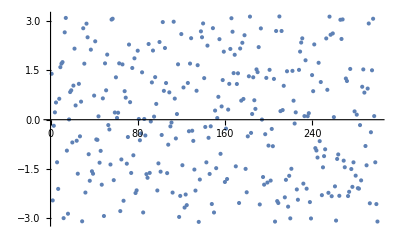

```mathematica
(*******************************************************************************************************************************************************************************************************************************)

SeedRandom[2];
(*J2seznam = RandomReal[{1,3000},100];*)
θseznam = RandomReal[{-π,π},300];

(*ListPlot[{J2seznam}]*)
ListPlot[{θseznam}]
```

```mathematica
σT=300;
σC =250;
F =12000;
a =2;


(* Izračun Lodejevega kota *)

θseznam;

(* Izračun J2 v oblik iseznama *)

h=((2^a-2(σT/σC)^a)/((2*σT/σC)^a-2))^(1/a);
k1 =(1-h)/(1+h)//N;

J2seznam = 3/4 (F/((Abs[Cos[θseznam]]-k1*Cos[θseznam])^a+(Abs[Cos[2 Pi /3+θseznam]]-k1*Cos[2 Pi /3+θseznam])^a+(Abs[Cos[2 Pi /3-θseznam]]-k1*Cos[2 Pi /3-θseznam])^a))^(2/a);

Sn= 2/(√3)*√J2seznam[[1]]*{{Cos[θseznam[[1]]]},{Cos[2 Pi /3-θseznam[[1]]]},{Cos[2 Pi /3+θseznam[[1]]]}}//Flatten;

Print["Seznam J2 = ",J2seznam," MPa^2"]
Print["\nLodejev kot seznam θ = ",θseznam*180/Pi," °\n"]
```

Seznam J2 = {5039.79,6076.33,6545.2,6458.8,5526.47,4857.45,6737.65,5185.02,5614.58,5974.93,6124.91,4742.61,5397.07,4685.72,4712.31,4913.04,6737.75,4803.02,4747.27,5052.9,4679.62,6712.27,5831.58,5176.49,5768.62,4684.59,5584.71,5437.67,4687.14,5066.94,5977.81,6653.7,4821.28,5908.25,4679.31,6423.93,6730.58,5514.71,5768.9,4969.88,6289.16,5282.99,5248.09,6677.57,4875.69,4707.8,6656.06,5153.9,4811.42,6006.46,4747.4,6661.15,6584.22,6265.21,4970.56,4705.98,4694.03,6377.16,6470.99,4848.83,6720.97,6486.58,6008.34,5070.16,4754.08,5901.66,6043.38,4772.52,5101.74,4925.4,5513.69,6532.37,5490.38,5689.59,5527.83,4682.73,6447.98,6632.98,6720.92,6738.1,6735.43,5214.34,5888.3,5140.63,4983.21,6735.27,5675.51,5815.29,6172.79,6497.03,5684.66,6721.65,4700.72,6737.78,6686.59,4856.58,5674.24,6718.76,4909.39,6347.07,5554.24,5726.44,4766.15,4762.62,6695.91,4692.49,5707.42,4922.85,4814.06,6506.38,6695.28,6652.53,4755.34,5170.7,5373.44,6568.97,5911.61,4778.78,6461.36,5573.09,5013.8,4692.24,5350.89,6553.66,5595.,4693.2,6103.88,5985.05,5998.98,6152.42,5165.78,5344.91,6716.7,4759.22,5819.63,4682.72,6326.85,5307.41,5903.95,4812.98,4815.72,6466.47,4860.04,6593.83,5433.24,5793.1,6509.57,5711.82,5059.94,4981.87,6319.33,5225.48,6723.33,5045.2,6093.69,4679.57,5933.71,4751.36,6734.21,6510.03,6338.17,6282.73,6235.65,4684.43,6719.,4688.48,5339.45,5084.35,6653.47,5086.93,4683.51,5070.47,5817.77,6709.23,5342.7,6408.77,5199.83,5694.32,5285.08,6664.58,5583.71,4896.87,4679.44,5940.14,6565.73,4849.97,5308.53,6171.27,5387.42,5154.69,6664.02,5665.85,5075.92,6738.07,6100.76,6654.24,5808.1,4824.81,6546.73,4876.45,5346.54,6410.29,6310.93,4848.96,4786.64,4684.85,5274.44,6008.89,5814.9,4679.31,6366.33,5275.08,6277.81,4680.1,6352.35,6352.45,5223.17,5438.01,5983.08,4737.22,5276.35,5256.07,5346.34,6659.44,6459.21,6734.26,6140.17,5342.4,6734.83,6391.05,6013.32,6606.21,6668.39,6291.69,6738.13,6671.07,6516.13,5910.42,4734.76,4959.75,4772.93,6524.04,4775.83,4714.56,4709.75,6061.71,5146.08,4706.78,6512.45,5159.36,4689.81,4742.03,6021.09,4734.44,6641.98,4679.47,5645.89,6439.08,5505.07,6701.94,6711.18,4695.46,4740.31,4679.52,6468.99,4709.84,6073.42,4703.95,4792.06,5152.65,4801.45,4727.07,6450.84,6682.78,5432.15,5298.02,6721.55,4859.87,6385.29,5966.24,6602.49,6737.27,6738.16,6583.57,6395.38,4685.25,5386.04,4823.17,4857.01,5018.86,4708.24,4814.76,5787.11,6006.76,5305.56,4694.16,6668.17,4858.2,5704.99,4685.21} MPa^2

Lodejev kot seznam θ = {80.0063,-140.598,-10.547,12.8095,29.944,-74.1807,-120.544,36.4528,91.5183,97.6044,100.287,-171.5,152.192,177.283,-53.8528,-163.798,0.489368,48.1522,51.1948,-39.6449,59.3897,123.797,24.8543,-36.6436,-94.0855,62.4646,-28.9773,31.4632,-176.999,159.279,97.6545,-126.899,167.319,143.549,-60.1335,-106.363,122.053,-89.8603,-94.0903,41.9818,136.549,-34.3785,-35.0939,5.82897,-74.8767,-54.2872,-113.2,37.1583,-167.761,98.1567,51.1865,113.417,-9.38168,-17.0312,-78.0386,174.472,175.89,-105.307,12.5101,73.839,3.09253,12.1192,98.1899,-159.196,-69.2325,96.3382,-141.189,49.7007,38.4014,-76.6152,-30.1568,130.907,30.5497,-92.7653,90.0785,-61.9852,106.929,-127.715,-123.097,120.21,1.23562,-35.8098,-23.8904,82.5329,-161.584,1.27095,-27.4691,-94.8705,-101.178,131.851,-92.6831,-3.03048,64.955,120.472,5.37274,74.1468,27.4903,-123.285,-76.0776,135.344,-90.517,-26.6202,170.056,50.2586,124.858,63.8899,-93.0624,-43.469,47.6413,-11.6076,-4.89485,-126.947,170.69,36.7744,-32.6278,9.85132,96.5088,-169.364,-132.747,149.17,-79.2941,56.1464,-153.051,-130.304,-148.807,63.9932,-20.0988,97.781,141.975,-19.2036,-36.886,-86.835,-123.457,50.4579,94.9437,-178.018,-104.228,153.892,143.623,167.69,72.4337,-12.6217,-74.2819,129.075,-31.5417,-94.4966,-11.5236,-146.864,159.46,-161.624,15.9288,-84.4293,2.87172,39.8488,140.284,-59.4407,23.1107,69.0645,118.518,-108.489,-15.5335,-103.321,17.6151,62.4269,123.265,176.754,153.269,81.1654,113.092,-81.2304,62.201,80.8121,-145.088,124.016,33.2072,133.986,36.1255,147.156,-85.6636,-126.432,-28.994,75.6429,179.591,-22.9996,9.94848,73.8848,33.8699,18.8502,87.6308,82.8598,126.457,-147.63,159.048,0.247222,-99.8443,-113.124,-25.2508,72.8357,-109.497,-45.0951,86.866,-106.049,-16.103,-46.1558,71.0442,-177.474,154.552,-141.8,-145.136,179.848,14.9296,154.539,16.7786,59.0369,-135.231,-104.771,84.3798,-151.457,-97.7467,-171.868,-85.4873,85.0718,33.1378,-6.65644,12.7994,-121.474,-139.431,86.787,118.637,134.385,141.722,-111.334,6.26074,103.502,-120.172,6.13772,11.349,-143.512,-172.041,77.7093,49.6782,131.135,-49.5215,-53.648,-65.9041,99.1384,-37.3398,65.6097,-131.447,-82.9674,-63.4735,-51.5388,141.585,52.0644,-127.371,179.55,147.962,-133.282,150.301,4.49619,-116.123,-175.695,-68.3447,-60.5116,-132.56,174.087,140.651,174.686,-71.3168,-82.8128,71.773,67.3893,-133.002,-125.57,88.4391,-85.9223,-116.96,-74.2754,14.5132,-97.4529,8.79054,-119.29,-120.107,-9.40219,-105.712,57.3866,87.6053,47.236,-45.8363,-79.435,54.2435,167.61,-145.604,-21.8379,86.0717,175.872,6.2709,-74.2101,-146.978,-177.394} °

```mathematica
Sa = Range[Length[θseznam]];
Print[Sa]
For[i=1,i<=Length[θseznam],i++,
Sa[[i]]=2/(√3)*√J2seznam[[i]]*{{Cos[θseznam[[i]]]},{Cos[2 Pi /3-θseznam[[i]]]},{Cos[2 Pi /3+θseznam[[i]]]}}//Flatten;
]
Print[Sa]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300}

{{14.2257,62.8015,-77.0272},{-69.5521,-14.7033,84.2554},{91.8398,-60.7285,-31.1113},{90.4899,-27.4269,-63.063},{74.3822,-0.0839695,-74.2982},{21.9384,-78.025,56.0866},{-48.1685,-46.6087,94.7772},{66.8787,9.34442,-76.2231},{-2.29256,76.0504,-73.7579},{-11.8114,82.5236,-70.7122},{-16.1375,85.0726,-68.9351},{-78.6469,29.1446,49.5023},{-75.0336,71.7884,3.24516},{-78.9531,42.7209,36.2322},{46.7559,-78.8101,32.0543},{-77.7221,19.3037,58.4184},{94.7787,-46.6883,-48.0904},{53.3891,24.9312,-78.3203},{49.8578,28.764,-78.6217},{63.203,-76.9549,13.7519},{40.2217,38.7643,-78.986},{-52.6235,94.3951,-41.7716},{80.0113,-7.90857,-72.1028},{66.659,-76.2705,9.61152},{-6.2482,-72.6343,78.8825},{36.5364,42.4229,-78.9593},{75.4891,-73.949,-1.54013},{72.6294,2.17425,-74.8036},{-78.9455,35.8889,43.0566},{-76.8775,63.6247,13.2527},{-11.8917,82.5732,-70.6815},{-56.5518,-36.9554,93.5072},{-78.2213,54.3537,23.8676},{-71.3923,81.3646,-9.97232},{39.3345,-78.9876,39.6532},{-26.0724,-63.867,89.9394},{-50.2741,94.671,-44.3969},{0.209043,-74.3654,74.1564},{-6.25573,-72.632,78.8877},{60.5118,16.8994,-77.4112},{-66.4784,87.7793,-21.3009},{69.2683,-75.6758,6.40745},{68.444,-75.8712,7.42717},{93.8701,-38.636,-55.2341},{21.0357,-77.9257,56.89},{46.2472,-78.8344,32.5873},{-37.1117,-56.4315,93.5432},{66.0662,10.3299,-76.3961},{-78.2748,24.4332,53.8416},{-12.697,83.0658,-70.3688},{49.8675,28.7535,-78.621},{-37.454,93.6206,-56.1666},{92.4428,-59.4486,-32.9942},{87.3899,-66.8783,-20.5116},{16.8722,-77.4075,60.5353},{-78.8442,46.0311,32.8131},{-78.9085,44.3646,34.5439},{-24.3432,-64.8525,89.1957},{90.6816,-27.916,-62.7656},{22.3799,55.6919,-78.0718},{94.5262,-42.8403,-51.6859},{90.9261,-28.5542,-62.372},{-12.7504,83.0981,-70.3478},{-76.8597,13.1393,63.7203},{28.2301,-78.585,50.3549},{-9.79298,81.2492,-71.4562},{-69.9471,-13.7495,83.6966},{51.5941,26.8913,-78.4854},{64.6348,12.0504,-76.6852},{18.7596,-77.6546,58.8951},{74.1366,-74.3713,0.234716},{-61.1133,91.6406,-30.5272},{73.6832,0.820901,-74.5041},{-4.20208,-73.2405,77.4426},{-0.117589,74.4081,-74.2905},{37.1141,-78.9693,41.8552},{-26.9999,90.3194,-63.3195},{-57.5294,-35.6616,93.191},{-51.6921,-42.8333,94.5255},{-47.6934,94.784,-47.0906},{94.7438,-45.6022,-49.1417},{67.6193,-76.0597,8.44039},{81.0147,-71.5842,-9.43047},{10.7592,65.7106,-76.4697},{-77.3381,16.3684,60.9697},{94.7414,-45.5504,-49.191},{77.1831,-73.3419,-3.84127},{-7.47624,-72.2446,79.7208},{-17.5877,-68.2826,85.8704},{-62.0989,91.0896,-28.9908},{-4.07546,-73.2763,77.3517},{94.5365,-51.6026,-42.9339},{33.5143,45.3582,-78.8725},{-48.0655,94.7792,-46.7137},{94.0069,-39.3468,-54.6601},{21.9823,56.0474,-78.0297},{77.1597,-3.80875,-73.3509},{-51.9441,-42.5489,94.493},{19.4667,-77.742,58.2753},{-65.4388,88.714,-23.2752},{-0.776458,-74.1355,74.912},{78.1173,-72.9659,-5.15138},{-78.5198,51.1816,27.3382},{50.9464,27.5925,-78.5389},{-54.0044,94.148,-40.1436},{34.8112,44.1056,-78.9168},{-4.66042,-73.1094,77.7698},{58.7981,-77.6685,18.8705},{53.9805,24.28,-78.2605},{91.2358,-61.8477,-29.3881},{94.1385,-54.0511,-40.0873},{-56.6105,-36.8788,93.4893},{-78.5782,50.4447,28.1335},{66.5083,9.79439,-76.3027},{71.2864,-75.167,3.88066},{92.2076,-32.2369,-59.9707},{-10.0639,81.4233,-71.3595},{-78.4515,26.4665,51.985},{-63.0011,-27.5292,90.5303},{-74.0211,75.2695,-1.24844},{15.1889,-77.1701,61.9813},{44.0628,34.8554,-78.9181},{-75.2942,4.49622,70.798},{-60.4658,-31.505,91.9709},{-73.8841,-1.79881,75.6829},{34.6858,44.2271,-78.913},{84.7197,-69.2076,-15.5121},{-12.0943,82.698,-70.6036},{-70.4516,82.9375,-12.4859},{85.5318,-68.566,-16.9659},{66.3798,-76.3301,9.95023},{4.66094,-75.3279,70.6669},{-52.1721,-42.2897,94.4618},{50.7148,27.8425,-78.5573},{-7.59112,79.7983,-72.2071},{-78.9693,37.1179,41.8514},{-22.5745,-65.8143,88.3888},{-75.5388,69.8291,5.70968},{-71.4341,81.2893,-9.85518},{-78.2664,53.9239,24.3424},{24.1842,54.0673,-78.2515},{90.6106,-62.8769,-27.7337},{21.8074,-78.0109,56.2034},{-59.1029,92.5909,-33.4879},{72.5388,-74.8288,2.28996},{-6.89029,-72.433,79.3233},{91.2855,-61.7607,-29.5247},{-73.0766,-4.77365,77.8502},{-76.9161,63.4157,13.5004},{-77.3455,16.4215,60.924},{88.2675,-22.3172,-65.9504},{8.10287,-75.9975,67.8947},{94.5618,-43.1729,-51.3889},{62.9683,14.029,-76.9973},{-69.3366,84.5484,-15.2118},{40.1609,-78.9862,38.8254},{81.8091,-10.6693,-71.1398},{28.4401,50.1596,-78.5997},{-45.2397,94.7256,-49.4859},{-29.5448,-61.7479,91.2927},{88.571,-65.6058,-22.9651},{-21.0877,-66.5873,87.675},{86.9068,-19.5566,-67.3502},{36.5819,42.3782,-78.9601},{-51.9171,94.4966,-42.5794},{-78.9384,43.3459,35.5924},{-75.3586,70.5467,4.81194},{12.6453,64.136,-76.7813},{-36.9407,93.5038,-56.563},{12.5562,-76.767,64.2108},{36.8542,42.1109,-78.965},{13.1288,63.7292,-76.858},{-72.2232,-7.54181,79.7651},{-52.9107,94.3492,-41.4384},{70.6183,4.72197,-75.3403},{-64.1972,89.699,-25.5018},{67.2557,8.88492,-76.1406},{-73.2061,77.5294,-4.32331},{6.34723,-75.6641,69.3168},{-55.9817,-37.6911,93.6728},{75.4701,-73.9553,-1.51489},{20.0363,57.774,-77.8103},{-78.9869,39.9815,39.0054},{81.921,-71.0746,-10.8464},{92.1576,-32.08,-60.0776},{22.3208,55.7448,-78.0656},{69.8545,5.67805,-75.5325},{85.8452,-17.541,-68.3041},{3.50358,71.5845,-75.0881},{10.3047,66.087,-76.3917},{-56.0121,93.6643,-37.6522},{-73.4102,-3.5946,77.0048},{-76.8279,63.8898,12.9381},{94.7836,-47.0376,-47.746},{-15.4201,-69.2473,84.6673},{-36.9912,-56.5243,93.5155},{79.5922,-72.3063,-7.28596},{23.6699,54.5323,-78.2022},{-31.1819,-60.6816,91.8635},{56.9226,-77.9216,20.999},{4.61606,70.7026,-75.3187},{-25.5585,-64.1646,89.7231},{88.1319,-66.1002,-22.0317},{55.6979,-78.0711,22.3732},{25.9508,52.4582,-78.409},{-78.9578,36.4624,42.4955},{-75.7237,69.0689,6.65488},{-70.3416,-12.766,83.1076},{-72.248,-7.46581,79.7138},{-78.9876,39.6754,39.3122},{89.0226,-23.9551,-65.0676},{-75.7202,69.0838,6.63634},{87.595,-20.925,-66.67},{40.6416,38.3417,-78.9834},{-65.3384,-23.4603,88.7987},{-23.4637,-65.3365,88.8003},{8.1728,67.8377,-76.0105},{-74.8017,2.16541,72.6363},{-12.0393,-70.6248,82.6641},{-78.6759,29.6016,49.0743},{6.59935,-75.713,69.1137},{7.19166,68.6349,-75.8266},{70.6983,4.62147,-75.3198},{93.5946,-56.2566,-37.338},{90.4964,-27.4434,-63.053},{-49.4739,-45.2524,94.7263},{-68.7323,-16.5954,85.3276},{4.73045,70.6116,-75.342},{-45.4155,94.7348,-49.3193},{-64.5698,89.4173,-24.8474},{-70.292,83.1834,-12.8914},{-34.1447,-58.6365,92.7811},{93.7307,-37.9601,-55.7707},{-21.385,87.8203,-66.4353},{-47.6382,-47.1462,94.7844},{93.7714,-38.153,-55.6185},{91.3878,-29.809,-61.5788},{-71.3711,-10.0315,81.4026},{-78.6892,29.8171,48.8721},{17.3108,60.1559,-77.4667},{51.6203,26.8629,-78.4831},{-61.3549,91.511,-30.1561},{51.8021,-78.4675,26.6654},{46.9957,-78.7981,31.8024},{32.3526,-78.824,46.4713},{-14.2781,84.0078,-69.7297},{65.8572,-76.4395,10.5823},{32.7137,46.1263,-78.8399},{-61.6812,-29.6493,91.3305},{10.1548,-76.3657,66.2109},{35.3165,-78.9312,43.6147},{49.4574,-78.65,29.1926},{-70.2042,83.3164,-13.1121},{48.845,29.8459,-78.6909},{-57.1196,-36.209,93.3286},{-78.9868,40.0303,38.9565},{-73.5485,76.6347,-3.08611},{-63.5256,-26.6533,90.179},{-74.4204,73.9699,0.450542},{94.2391,-40.7019,-53.5372},{-41.6503,-52.7283,94.3787},{-78.9008,34.3065,44.5943},{29.3376,-78.6593,49.3217},{38.8825,-78.9865,40.104},{-62.815,-27.8352,90.6502},{-78.8234,46.4822,32.3412},{-69.5879,84.2061,-14.6182},{-78.8552,45.7792,33.0759},{25.6056,-78.3797,52.774},{10.3701,-76.403,66.0329},{25.0263,53.3025,-78.3289},{30.5229,48.2078,-78.7306},{-63.2524,-27.1121,90.3645},{-54.9091,-39.0399,93.9491},{2.31827,72.5167,-74.8349},{5.97655,-75.5915,69.615},{-42.9197,-51.6152,94.535},{21.8159,-78.0118,56.1959},{89.3255,-24.6375,-64.688},{-11.569,-70.8044,82.3734},{92.7239,-33.9442,-58.7796},{-46.3689,-48.4027,94.7716},{-47.5462,-47.2387,94.7849},{92.4328,-59.4716,-32.9612},{-25.006,-64.4801,89.4861},{42.5988,36.3569,-78.9557},{3.54077,71.5551,-75.0959},{54.4493,23.7618,-78.2111},{56.0669,-78.0273,21.9604},{14.9987,-77.1423,62.1436},{46.2984,32.5337,-78.8321},{-78.2567,54.0168,24.2399},{-72.4828,-6.73301,79.2158},{83.0711,-70.3653,-12.7058},{5.76205,69.7871,-75.5492},{-78.9078,44.386,34.5218},{93.7273,-37.9441,-55.7832},{21.9004,-78.0209,56.1205},{-73.1275,-4.59768,77.7252},{-78.9559,36.3656,42.5903}}

```mathematica
CPB06[s1_, s2_, s3_] := (Abs[s1]-k1 s1)^a+(Abs[s2]-k1 s2)^a+(Abs[s3]-k1 s3)^a-F
CPB063D= ContourPlot3D[CPB06[s1, s2, s3] == 0, {s1, -200, 200}, {s2, -200, 200},{s3, -200, 200},PlotPoints->15,ImageSize->{400,400},ContourStyle->Opacity[0.005],AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,AxesLabel->{Style["S1",Red,FontFamily->"Zapfino",FontSize->24],Style["S2",Red,FontFamily->"Zapfino",FontSize->24],Style["S3",Red,FontFamily->"Zapfino",FontSize->24]}];
Tocke3D1={{S1,S2,S3}};
Tocke3D2={{Sn[[1]],Sn[[2]],Sn[[3]]}};                (* PAZI NA VRSTNI RED, DODAJ SORT ČE JE PRAVILNO, PREVERI*)

Show[CPB063D,Graphics3D[{Blue,PointSize[.01],Point[Sa]}],ViewProjection->"Orthographic",PlotRange->All,ViewPoint->{1,1,1},AxesOrigin->{0,0,0}]
```

-Graphics3D-